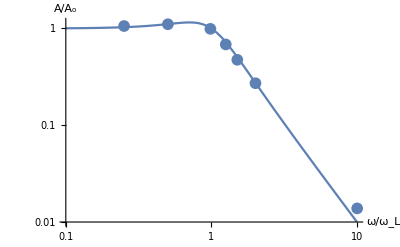

```mathematica
AjwA[omega_] := 1/Sqrt[(1-(omega)^2)^2+(omega/ql)^2];
ol=2 Pi*39.79;fl = 39.79;ao=2*2.17;
ql=1;
data = {{10,4.6},{20,4.8},{39.2,4.3},{50,2.97},{60,2.06},{80,1.18},{400,0.06}};
data2 =data.{{1/fl,0},{0,1/ao}};
fig1=LogLogPlot[Abs[AjwA[x]],{x,0.1,10},AxesOrigin->{0.1,0.01},AxesLabel->{"ω/ω_L","A/A_o"}];
fig2=ListLogLogPlot[data2,PlotMarkers->{Automatic,12}];
Show[fig1,fig2]
```